## Information and copyright

Simulation code associated with “Projecting the transmission dynamics of SARS-CoV-2 through the post-pandemic period”, 
by S.M. Kissler*, C. Tedijanto*, E. Goldstein, Y.H. Grad, and M. Lipsitch
* denotes equal contribution
Correspondence: skissler@hsph.harvard.edu

Last modified: 22 March 2020

    This program is free software: you can redistribute it and/or modify
    it under the terms of the GNU General Public License as published by
    the Free Software Foundation, either version 3 of the License, or
    (at your option) any later version.

    This program is distributed in the hope that it will be useful,
    but WITHOUT ANY WARRANTY; without even the implied warranty of
    MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the
    GNU General Public License for more details.

    You should have received a copy of the GNU General Public License
    along with this program.  If not, see <https://www.gnu.org/licenses/>.

## Define forcing functions:

```mathematica
(*Seasonality function*)
betaval[t_,amplitude_,baseline_,phival_,gammaval_]:=gammaval*(amplitude/2*Cos[2*Pi*(t-phival)/52]+(amplitude/2+baseline))

(*Function for simulating importation of strain 1*)
p1[t_,kappaval_,importtime1_,importlength_]:=If[t>importtime1&& t≤(importtime1+importlength),kappaval,0]

(*Function for simulating importation of strain 2*)
p2[t_,kappaval_,importtime2_,importlength_]:=If[t>importtime2&& t≤(importtime2+importlength),kappaval,0]

(*Function for simulating importation of strain 3*)
p3[t_,kappaval_,importtime3_,importlength_]:=If[t>importtime3&& t≤(importtime3+importlength),kappaval,0]
```

## Define model functions:

```mathematica
S1S2S3c1[t]:=betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2S3[t]+p1[t,kappaval,importtime1,importlength]*S1S2S3[t]

S1S2S3c2[t]:=betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2S3[t]+p2[t,kappaval,importtime2,importlength]*S1S2S3[t]

S1S2S3c3[t]:=betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1S2S3[t]+p3[t,kappaval,importtime3,importlength]*S1S2S3[t]

S1S2E3c1[t]:=(1-chi31val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2E3[t]+(1-chi31val)*p1[t,kappaval,importtime1,importlength]*S1S2E3[t]

S1S2E3c2[t]:=(1-chi32val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2E3[t]+(1-chi32val)*p2[t,kappaval,importtime2,importlength]*S1S2E3[t]

S1S2E3c3[t]:=nuval*S1S2E3[t]

S1S2I3c1[t]:=(1-chi31val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2I3[t]+(1-chi31val)*p1[t,kappaval,importtime1,importlength]*S1S2I3[t]

S1S2I3c2[t]:=(1-chi32val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2I3[t]+(1-chi32val)*p2[t,kappaval,importtime2,importlength]*S1S2I3[t]

S1S2I3c3[t]:=gammaval*S1S2I3[t]

S1S2R3c1[t]:=(1-chi31val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2R3[t]+(1-chi31val)*p1[t,kappaval,importtime1,importlength]*S1S2R3[t]

S1S2R3c2[t]:=(1-chi32val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2R3[t]+(1-chi32val)*p2[t,kappaval,importtime2,importlength]*S1S2R3[t]

S1S2R3c3[t]:=sigma3val*S1S2R3[t]

S1E2S3c1[t]:=(1-chi21val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2S3[t]+(1-chi21val)*p1[t,kappaval,importtime1,importlength]*S1E2S3[t]

S1E2S3c2[t]:=nuval*S1E2S3[t]

S1E2S3c3[t]:=(1-chi23val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1E2S3[t]+(1-chi23val)*p3[t,kappaval,importtime3,importlength]*S1E2S3[t]

S1E2E3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2E3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1E2E3[t]

S1E2E3c2[t]:=nuval*S1E2E3[t]

S1E2E3c3[t]:=nuval*S1E2E3[t]

S1E2I3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2I3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1E2I3[t]

S1E2I3c2[t]:=nuval*S1E2I3[t]

S1E2I3c3[t]:=gammaval*S1E2I3[t]

S1E2R3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2R3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1E2R3[t]

S1E2R3c2[t]:=nuval*S1E2R3[t]

S1E2R3c3[t]:=sigma3val*S1E2R3[t]

S1I2S3c1[t]:=(1-chi21val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2S3[t]+(1-chi21val)*p1[t,kappaval,importtime1,importlength]*S1I2S3[t]

S1I2S3c2[t]:=gammaval*S1I2S3[t]

S1I2S3c3[t]:=(1-chi23val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1I2S3[t]+(1-chi23val)*p3[t,kappaval,importtime3,importlength]*S1I2S3[t]

S1I2E3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2E3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1I2E3[t]

S1I2E3c2[t]:=gammaval*S1I2E3[t]

S1I2E3c3[t]:=nuval*S1I2E3[t]

S1I2I3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2I3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1I2I3[t]

S1I2I3c2[t]:=gammaval*S1I2I3[t]

S1I2I3c3[t]:=gammaval*S1I2I3[t]

S1I2R3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2R3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1I2R3[t]

S1I2R3c2[t]:=gammaval*S1I2R3[t]

S1I2R3c3[t]:=sigma3val*S1I2R3[t]

S1R2S3c1[t]:=(1-chi21val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2S3[t]+(1-chi21val)*p1[t,kappaval,importtime1,importlength]*S1R2S3[t]

S1R2S3c2[t]:=sigma2val*S1R2S3[t]

S1R2S3c3[t]:=(1-chi23val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1R2S3[t]+(1-chi23val)*p3[t,kappaval,importtime3,importlength]*S1R2S3[t]

S1R2E3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2E3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1R2E3[t]

S1R2E3c2[t]:=sigma2val*S1R2E3[t]

S1R2E3c3[t]:=nuval*S1R2E3[t]

S1R2I3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2I3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1R2I3[t]

S1R2I3c2[t]:=sigma2val*S1R2I3[t]

S1R2I3c3[t]:=gammaval*S1R2I3[t]

S1R2R3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2R3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1R2R3[t]

S1R2R3c2[t]:=sigma2val*S1R2R3[t]

S1R2R3c3[t]:=sigma3val*S1R2R3[t]

E1S2S3c1[t]:=nuval*E1S2S3[t]

E1S2S3c2[t]:=(1-chi12val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2S3[t]+(1-chi12val)*p2[t,kappaval,importtime2,importlength]*E1S2S3[t]

E1S2S3c3[t]:=(1-chi13val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1S2S3[t]+(1-chi13val)*p3[t,kappaval,importtime3,importlength]*E1S2S3[t]

E1S2E3c1[t]:=nuval*E1S2E3[t]

E1S2E3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2E3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*E1S2E3[t]

E1S2E3c3[t]:=nuval*E1S2E3[t]

E1S2I3c1[t]:=nuval*E1S2I3[t]

E1S2I3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2I3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*E1S2I3[t]

E1S2I3c3[t]:=gammaval*E1S2I3[t]

E1S2R3c1[t]:=nuval*E1S2R3[t]

E1S2R3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2R3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*E1S2R3[t]

E1S2R3c3[t]:=sigma3val*E1S2R3[t]

E1E2S3c1[t]:=nuval*E1E2S3[t]

E1E2S3c2[t]:=nuval*E1E2S3[t]

E1E2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1E2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*E1E2S3[t]

E1E2E3c1[t]:=nuval*E1E2E3[t]

E1E2E3c2[t]:=nuval*E1E2E3[t]

E1E2E3c3[t]:=nuval*E1E2E3[t]

E1E2I3c1[t]:=nuval*E1E2I3[t]

E1E2I3c2[t]:=nuval*E1E2I3[t]

E1E2I3c3[t]:=gammaval*E1E2I3[t]

E1E2R3c1[t]:=nuval*E1E2R3[t]

E1E2R3c2[t]:=nuval*E1E2R3[t]

E1E2R3c3[t]:=sigma3val*E1E2R3[t]

E1I2S3c1[t]:=nuval*E1I2S3[t]

E1I2S3c2[t]:=gammaval*E1I2S3[t]

E1I2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1I2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*E1I2S3[t]

E1I2E3c1[t]:=nuval*E1I2E3[t]

E1I2E3c2[t]:=gammaval*E1I2E3[t]

E1I2E3c3[t]:=nuval*E1I2E3[t]

E1I2I3c1[t]:=nuval*E1I2I3[t]

E1I2I3c2[t]:=gammaval*E1I2I3[t]

E1I2I3c3[t]:=gammaval*E1I2I3[t]

E1I2R3c1[t]:=nuval*E1I2R3[t]

E1I2R3c2[t]:=gammaval*E1I2R3[t]

E1I2R3c3[t]:=sigma3val*E1I2R3[t]

E1R2S3c1[t]:=nuval*E1R2S3[t]

E1R2S3c2[t]:=sigma2val*E1R2S3[t]

E1R2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1R2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*E1R2S3[t]

E1R2E3c1[t]:=nuval*E1R2E3[t]

E1R2E3c2[t]:=sigma2val*E1R2E3[t]

E1R2E3c3[t]:=nuval*E1R2E3[t]

E1R2I3c1[t]:=nuval*E1R2I3[t]

E1R2I3c2[t]:=sigma2val*E1R2I3[t]

E1R2I3c3[t]:=gammaval*E1R2I3[t]

E1R2R3c1[t]:=nuval*E1R2R3[t]

E1R2R3c2[t]:=sigma2val*E1R2R3[t]

E1R2R3c3[t]:=sigma3val*E1R2R3[t]

I1S2S3c1[t]:=gammaval*I1S2S3[t]

I1S2S3c2[t]:=(1-chi12val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2S3[t]+(1-chi12val)*p2[t,kappaval,importtime2,importlength]*I1S2S3[t]

I1S2S3c3[t]:=(1-chi13val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1S2S3[t]+(1-chi13val)*p3[t,kappaval,importtime3,importlength]*I1S2S3[t]

I1S2E3c1[t]:=gammaval*I1S2E3[t]

I1S2E3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2E3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*I1S2E3[t]

I1S2E3c3[t]:=nuval*I1S2E3[t]

I1S2I3c1[t]:=gammaval*I1S2I3[t]

I1S2I3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2I3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*I1S2I3[t]

I1S2I3c3[t]:=gammaval*I1S2I3[t]

I1S2R3c1[t]:=gammaval*I1S2R3[t]

I1S2R3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2R3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*I1S2R3[t]

I1S2R3c3[t]:=sigma3val*I1S2R3[t]

I1E2S3c1[t]:=gammaval*I1E2S3[t]

I1E2S3c2[t]:=nuval*I1E2S3[t]

I1E2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1E2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*I1E2S3[t]

I1E2E3c1[t]:=gammaval*I1E2E3[t]

I1E2E3c2[t]:=nuval*I1E2E3[t]

I1E2E3c3[t]:=nuval*I1E2E3[t]

I1E2I3c1[t]:=gammaval*I1E2I3[t]

I1E2I3c2[t]:=nuval*I1E2I3[t]

I1E2I3c3[t]:=gammaval*I1E2I3[t]

I1E2R3c1[t]:=gammaval*I1E2R3[t]

I1E2R3c2[t]:=nuval*I1E2R3[t]

I1E2R3c3[t]:=sigma3val*I1E2R3[t]

I1I2S3c1[t]:=gammaval*I1I2S3[t]

I1I2S3c2[t]:=gammaval*I1I2S3[t]

I1I2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1I2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*I1I2S3[t]

I1I2E3c1[t]:=gammaval*I1I2E3[t]

I1I2E3c2[t]:=gammaval*I1I2E3[t]

I1I2E3c3[t]:=nuval*I1I2E3[t]

I1I2I3c1[t]:=gammaval*I1I2I3[t]

I1I2I3c2[t]:=gammaval*I1I2I3[t]

I1I2I3c3[t]:=gammaval*I1I2I3[t]

I1I2R3c1[t]:=gammaval*I1I2R3[t]

I1I2R3c2[t]:=gammaval*I1I2R3[t]

I1I2R3c3[t]:=sigma3val*I1I2R3[t]

I1R2S3c1[t]:=gammaval*I1R2S3[t]

I1R2S3c2[t]:=sigma2val*I1R2S3[t]

I1R2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1R2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*I1R2S3[t]

I1R2E3c1[t]:=gammaval*I1R2E3[t]

I1R2E3c2[t]:=sigma2val*I1R2E3[t]

I1R2E3c3[t]:=nuval*I1R2E3[t]

I1R2I3c1[t]:=gammaval*I1R2I3[t]

I1R2I3c2[t]:=sigma2val*I1R2I3[t]

I1R2I3c3[t]:=gammaval*I1R2I3[t]

I1R2R3c1[t]:=gammaval*I1R2R3[t]

I1R2R3c2[t]:=sigma2val*I1R2R3[t]

I1R2R3c3[t]:=sigma3val*I1R2R3[t]

R1S2S3c1[t]:=sigma1val*R1S2S3[t]

R1S2S3c2[t]:=(1-chi12val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2S3[t]+(1-chi12val)*p2[t,kappaval,importtime2,importlength]*R1S2S3[t]

R1S2S3c3[t]:=(1-chi13val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1S2S3[t]+(1-chi13val)*p3[t,kappaval,importtime3,importlength]*R1S2S3[t]

R1S2E3c1[t]:=sigma1val*R1S2E3[t]

R1S2E3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2E3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*R1S2E3[t]

R1S2E3c3[t]:=nuval*R1S2E3[t]

R1S2I3c1[t]:=sigma1val*R1S2I3[t]

R1S2I3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2I3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*R1S2I3[t]

R1S2I3c3[t]:=gammaval*R1S2I3[t]

R1S2R3c1[t]:=sigma1val*R1S2R3[t]

R1S2R3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2R3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*R1S2R3[t]

R1S2R3c3[t]:=sigma3val*R1S2R3[t]

R1E2S3c1[t]:=sigma1val*R1E2S3[t]

R1E2S3c2[t]:=nuval*R1E2S3[t]

R1E2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1E2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*R1E2S3[t]

R1E2E3c1[t]:=sigma1val*R1E2E3[t]

R1E2E3c2[t]:=nuval*R1E2E3[t]

R1E2E3c3[t]:=nuval*R1E2E3[t]

R1E2I3c1[t]:=sigma1val*R1E2I3[t]

R1E2I3c2[t]:=nuval*R1E2I3[t]

R1E2I3c3[t]:=gammaval*R1E2I3[t]

R1E2R3c1[t]:=sigma1val*R1E2R3[t]

R1E2R3c2[t]:=nuval*R1E2R3[t]

R1E2R3c3[t]:=sigma3val*R1E2R3[t]

R1I2S3c1[t]:=sigma1val*R1I2S3[t]

R1I2S3c2[t]:=gammaval*R1I2S3[t]

R1I2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1I2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*R1I2S3[t]

R1I2E3c1[t]:=sigma1val*R1I2E3[t]

R1I2E3c2[t]:=gammaval*R1I2E3[t]

R1I2E3c3[t]:=nuval*R1I2E3[t]

R1I2I3c1[t]:=sigma1val*R1I2I3[t]

R1I2I3c2[t]:=gammaval*R1I2I3[t]

R1I2I3c3[t]:=gammaval*R1I2I3[t]

R1I2R3c1[t]:=sigma1val*R1I2R3[t]

R1I2R3c2[t]:=gammaval*R1I2R3[t]

R1I2R3c3[t]:=sigma3val*R1I2R3[t]

R1R2S3c1[t]:=sigma1val*R1R2S3[t]

R1R2S3c2[t]:=sigma2val*R1R2S3[t]

R1R2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1R2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*R1R2S3[t]

R1R2E3c1[t]:=sigma1val*R1R2E3[t]

R1R2E3c2[t]:=sigma2val*R1R2E3[t]

R1R2E3c3[t]:=nuval*R1R2E3[t]

R1R2I3c1[t]:=sigma1val*R1R2I3[t]

R1R2I3c2[t]:=sigma2val*R1R2I3[t]

R1R2I3c3[t]:=gammaval*R1R2I3[t]

R1R2R3c1[t]:=sigma1val*R1R2R3[t]

R1R2R3c2[t]:=sigma2val*R1R2R3[t]

R1R2R3c3[t]:=sigma3val*R1R2R3[t]
```

## Set default parameter values:

```mathematica
sigma1val = 1/40; (*Waning immunity rate, strain 1, weeks; default 1/40*)
sigma2val = 1/38; (*Waning immunity rate, strain 1, weeks; default 1/40*)
sigma3val = 1/104; (*Waning immunity rate, strain 1, weeks; default 1/40*)
nuval = 1/(5/7);  (*Rate of progression to infection, weeks; default 1/1*)
gammaval = 1/(4.9/7); (*Rate of recovery, weeks; default 1/1*)
chi12val = 0.74; (*Cross immunity, strain 1 to 2*)
chi21val = 0.5; (*Cross immunity, strain 2 to 1*)
chi13val=0.0; (*Cross immunity, strain 1 to 2*)
chi31val=0.7; (*Cross immunity, strain 3 to 1*)
chi23val=0.0; (*Cross immunity, strain 2 to 3*)
chi32val=0.7; (*Cross immunity, strain 3 to 2*)
amplitude=0.66; (*Amplitude of seasonal R0*)
baseline=1.4; (*Baseline Ro value*)
phival=-3.8; (*Phase shift for seasonal R0 (weeks)*)
kappaval = 0.01; (*Boost from importations*)
importtime1 = 0; (*Importation time for strain 1, weeks*)
importtime2 = 52;  (*Importation time for strain 2, weeks*)
importtime3= 52*100(*52*24+12*);  (*Importation time for strain 3, weeks*)
importlength = 0.5; (*How long does an importation boost transmission, in weeks?*)
muval = 1/(80*52); (* birth rate, in weeks *) 
f = 1; (*Seasonality factor (1 = full seasonality, 0 = no seasonality so that R0 stays fixed at its maximal wintertime value*)
```

```mathematica
scalingfactor = 0.075; (*Conversion between prevalence and (% positive * % ILI) *)
```

```mathematica
tmax = 52*30; (*Simulation timespan, weeks*)
```

```mathematica
plotwindow = {52*20.5, 52*27.5}; (*Time span for plotting*)
plotrangemax = 0.8; (*Max plotting value *)
importbarchar = {Black, Thick}; (*For plotting the bar marking the importation time*)
yearbarchar = {Gray, Thin}; (*For marking years*)
fs = 18; (*Plot font size*)
imsz = 400; (*plot image size*)
oc43char = {Blue,Thickness[0.008], Opacity[0.5]}; (*Plotting characteristics for HCoV-OC43*)
hku1char = {Red, Thickness[0.008], Opacity[0.5]};(*Plotting characteristics for HCoV-HKU1*)
ncovchar={Black, Thickness[0.008], Opacity[0.5]};(*Plotting characteristics for HCoV-SARS-CoV-2*)
totalchar={Black, Thickness[0.004], Opacity[0.5],Dashed};(*Plotting characteristics for the total prevalence curve*)
```

## Run some scenarios:

### 70/0 | 104 | w4:

#### Define parameter values:

```mathematica
chi31val=0.7;
chi32val = 0.7;
chi13val = 0;
chi23val = 0;
sigma3val = 1/104;
importtime3 = 52*22 + 4;
```

#### Run the model:

```mathematica
sol = NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf},
{t, 0, tmax}
];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])},
{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])
}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,False}, PlotRangePadding->None, BaseStyle->FontSize->fs, FrameTicks->{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}],Automatic}, FrameLabel->{"Year","%Positive x %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2","Total"}, PlotStyle->{oc43char, hku1char,ncovchar,totalchar}];
```

#### Save output:

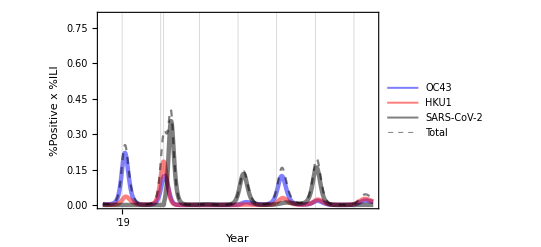

```mathematica
figinvasion
```

### 70/0 | 104 | w26:

#### Define parameter values:

```mathematica
chi31val=0.7;
chi32val = 0.7;
chi13val = 0;
chi23val = 0;
sigma3val = 1/104;
importtime3 = 52*22 + 26;
```

#### Run the model:

```mathematica
sol = NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf},
{t, 0, tmax}
];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])},
{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])
}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,False}, PlotRangePadding->None, BaseStyle->FontSize->fs, FrameTicks->{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}],Automatic}, FrameLabel->{"Year","%Positive x %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2","Total"}, PlotStyle->{oc43char, hku1char,ncovchar,totalchar}];
```

#### Save output:

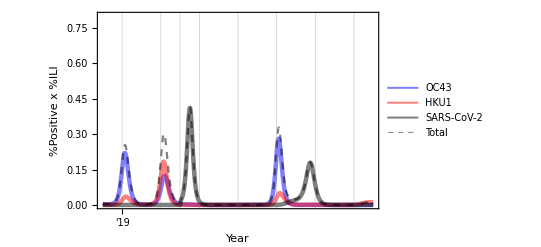

```mathematica
figinvasion
```

### 70/0 | ∞ | w12:

#### Define parameter values:

```mathematica
chi31val=0.7;
chi32val = 0.7;
chi13val = 0;
chi23val = 0;
sigma3val = 1/Infinity;
importtime3 = 52*22 + 12;
```

#### Run the model:

```mathematica
sol = NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf},
{t, 0, tmax}
];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])},
{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])
}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,False}, PlotRangePadding->None, BaseStyle->FontSize->fs, FrameTicks->{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}],Automatic}, FrameLabel->{"Year","%Positive x %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2","Total"}, PlotStyle->{oc43char, hku1char,ncovchar,totalchar}];
```

#### Save output:

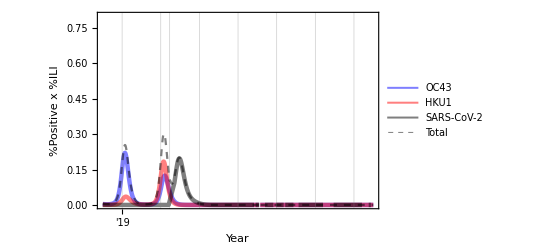

```mathematica
figinvasion
```

### 30/0 | 40 | w12:

#### Define parameter values:

```mathematica
chi31val=0.3;
chi32val = 0.3;
chi13val = 0;
chi23val = 0;
sigma3val = 1/40;
importtime3 = 52*22 + 12;
```

#### Run the model:

```mathematica
sol = NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf},
{t, 0, tmax}
];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])},
{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])
}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,False}, PlotRangePadding->None, BaseStyle->FontSize->fs, FrameTicks->{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}],Automatic}, FrameLabel->{"Year","%Positive x %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2","Total"}, PlotStyle->{oc43char, hku1char,ncovchar,totalchar}];
```

#### Save output:

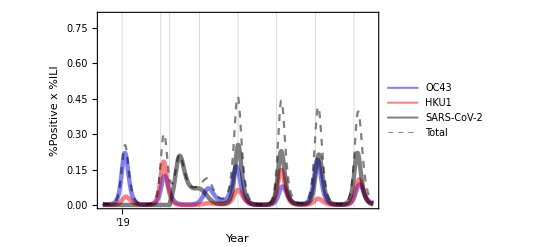

```mathematica
figinvasion
```

### 30/0 | 40 | w36:

#### Define parameter values:

```mathematica
chi31val=0.3;
chi32val = 0.3;
chi13val = 0;
chi23val = 0;
sigma3val = 1/40;
importtime3 = 52*22 + 36;
```

#### Run the model:

```mathematica
sol = NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf},
{t, 0, tmax}
];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])},
{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])
}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,False}, PlotRangePadding->None, BaseStyle->FontSize->fs, FrameTicks->{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}],Automatic}, FrameLabel->{"Year","%Positive x %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2","Total"}, PlotStyle->{oc43char, hku1char,ncovchar,totalchar}];
```

#### Save output:

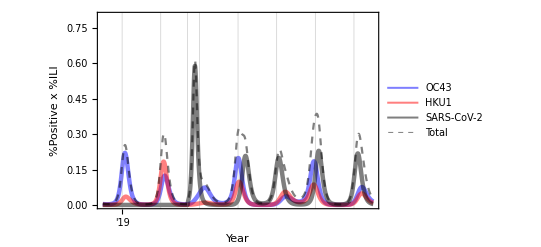

```mathematica
figinvasion
```

### 30/30 | 104 | w32:

#### Define parameter values:

```mathematica
chi31val=0.3;
chi32val = 0.3;
chi13val = 0.3;
chi23val = 0.3;
sigma3val = 1/104;
importtime3 = 52*22 + 32;
```

#### Run the model:

```mathematica
sol = NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf},
{t, 0, tmax}
];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])},
{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])
}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,False}, PlotRangePadding->None, BaseStyle->FontSize->fs, FrameTicks->{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}],Automatic}, FrameLabel->{"Year","%Positive x %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2","Total"}, PlotStyle->{oc43char, hku1char,ncovchar,totalchar}];
```

#### Save output:

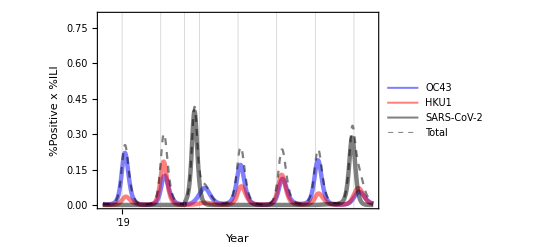

```mathematica
figinvasion
```

## Tables of cumulative infections and peak sizes:

```mathematica
χ3Xvals={{0.7, 0},{0.7, 0.3},{0.3,0},{0,0}};
σ3vals = {{1/40}, {1/104}, {0}};
importtime3vals = {{52*22+4},{52*22+16},{52*22+28},{52*22+40}}; 
fvals = {{0}, {0.5}, {1}};
```

```mathematica
paramsets = Partition[Flatten[Table[Join[χ3X, σ3, importtime3, f], {χ3X, χ3Xvals}, {σ3, σ3vals}, {importtime3, importtime3vals},{f, fvals}]],5];
```

```mathematica
cuminfvec = {};
cuminfnCoVvec = {};
peakinfectedvec = {};
peakinfectednCoVvec = {};
```

```mathematica
Do[
chi31val = params⟦1⟧;
chi32val = params⟦1⟧;
chi13val = params⟦2⟧;
chi23val = params⟦2⟧;
sigma3val = params⟦3⟧;
importtime3 = params⟦4⟧;
f = params⟦5⟧;

sol = NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
cuminfnCoV'[t]== S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0, cuminfnCoV[0]==0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf, cuminfnCoV},
{t, 0, tmax}
];

cuminftags = Flatten[Table[Evaluate[scalingfactor*cuminf[t]
/.sol],{t,plotwindow⟦1⟧,plotwindow⟦2⟧, 52}]];
cuminfnCoVtags = Flatten[Table[Evaluate[scalingfactor*cuminfnCoV[t]
/.sol],{t,plotwindow⟦1⟧,plotwindow⟦2⟧, 52}]];

cuminfbyseason = Drop[cuminftags,1] - Drop[cuminftags,-1];
cuminfnCoVbyseason = Drop[cuminfnCoVtags,1] - Drop[cuminfnCoVtags,-1];

cuminfvec = Join[cuminfvec, {cuminfbyseason}];
cuminfnCoVvec = Join[cuminfnCoVvec, {cuminfnCoVbyseason}];

dailyinfected = Flatten[Table[Evaluate[scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])/.sol],{t,plotwindow⟦1⟧+1/7,plotwindow⟦2⟧, 1/7}]];

dailyinfectednCoV = Flatten[Table[Evaluate[scalingfactor*(S1S2I3[t] + S1E2I3[t] + S1I2I3[t] + S1R2I3[t] + E1S2I3[t] + E1E2I3[t] + E1I2I3[t] + E1R2I3[t] + I1S2I3[t] + I1E2I3[t] + I1I2I3[t] + I1R2I3[t] + R1S2I3[t] + R1E2I3[t] + R1I2I3[t] + R1R2I3[t])/.sol],{t,plotwindow⟦1⟧+1/7,plotwindow⟦2⟧, 1/7}]];

peakinfected = Max[#]&/@Partition[dailyinfected,Length[dailyinfected]/7];
peakinfectedvec = Join[peakinfectedvec,{ peakinfected}];

peakinfectednCoV = Max[#]&/@Partition[dailyinfectednCoV,Length[dailyinfectednCoV]/7];
peakinfectednCoVvec = Join[peakinfectednCoVvec,{ peakinfectednCoV}];

(*Print[params];*)

,{params, paramsets}]
```

```mathematica
Join[{{"χ3X", "χX3", "σ3", "importtime3","f", "19", "20", "21", "22", "23", "24", "25"}},Table[Join[paramsets⟦i⟧, 100*cuminfvec⟦i⟧],{i,Length[paramsets]}]]//TableForm;
```

```mathematica
Join[{{"χ3X", "χX3", "σ3", "importtime3","f", "19", "20", "21", "22", "23", "24", "25"}},Table[Join[paramsets⟦i⟧, 100*cuminfnCoVvec⟦i⟧],{i,Length[paramsets]}]]//TableForm;
```

```mathematica
Join[{{"χ3X", "χX3", "σ3", "importtime3", "19", "20", "21", "22", "23", "24", "25"}},Table[Join[paramsets⟦i⟧, 100*peakinfectedvec⟦i⟧],{i,Length[paramsets]}]]//TableForm;
```

```mathematica
Join[{{"χ3X", "χX3", "σ3", "importtime3", "19", "20", "21", "22", "23", "24", "25"}},Table[Join[paramsets⟦i⟧, 100*peakinfectednCoVvec⟦i⟧],{i,Length[paramsets]}]]//TableForm
```

χ3X | χX3 | σ3 | importtime3 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 
0.7 | 0 | 1/40 | 1148 | 0 | 0. | 0.627689 | 0.168377 | 0.0949357 | 0.0753667 | 0.0691173 | 0.0669786
0.7 | 0 | 1/40 | 1148 | 0.5 | 0. | 0.501762 | 0.13517 | 0.130892 | 0.164467 | 0.177552 | 0.180958
0.7 | 0 | 1/40 | 1148 | 1 | 0. | 0.361707 | 0.157245 | 0.228484 | 0.223636 | 0.216788 | 0.219881
0.7 | 0 | 1/40 | 1160 | 0 | 0. | 0.627692 | 0.570488 | 0.168184 | 0.0851471 | 0.0691176 | 0.0669787
0.7 | 0 | 1/40 | 1160 | 0.5 | 0. | 0.402484 | 0.421003 | 0.107093 | 0.158061 | 0.176877 | 0.18156
0.7 | 0 | 1/40 | 1160 | 1 | 0. | 0.142478 | 0.242761 | 0.2679 | 0.227844 | 0.212698 | 0.221133
0.7 | 0 | 1/40 | 1172 | 0 | 0. | 0. | 0.627691 | 0.168379 | 0.0949362 | 0.0753667 | 0.0684039
0.7 | 0 | 1/40 | 1172 | 0.5 | 0. | 0. | 0.52876 | 0.222627 | 0.193706 | 0.185042 | 0.182106
0.7 | 0 | 1/40 | 1172 | 1 | 0. | 0. | 0.462711 | 0.280515 | 0.20855 | 0.215282 | 0.222544
0.7 | 0 | 1/40 | 1184 | 0 | 0. | 0. | 0.627692 | 0.168377 | 0.0949355 | 0.0753665 | 0.0691174
0.7 | 0 | 1/40 | 1184 | 0.5 | 0. | 0. | 0.623998 | 0.231831 | 0.173023 | 0.172909 | 0.177904
0.7 | 0 | 1/40 | 1184 | 1 | 0. | 0. | 0.620668 | 0.163837 | 0.184226 | 0.239107 | 0.217288
0.7 | 0 | 1/104 | 1148 | 0 | 0. | 0.616921 | 0.00441861 | 0.159583 | 0.153446 | 0.0751188 | 0.047171
0.7 | 0 | 1/104 | 1148 | 0.5 | 0. | 0.492546 | 0.00858174 | 0.0872222 | 0.0644619 | 0.0678825 | 0.0378516
0.7 | 0 | 1/104 | 1148 | 1 | 0. | 0.355026 | 0.0153462 | 0.131092 | 0.0101612 | 0.158537 | 0.000499388
0.7 | 0 | 1/104 | 1160 | 0 | 0. | 0.616924 | 0.553492 | 0.0301463 | 0.159454 | 0.0750845 | 0.0417953
0.7 | 0 | 1/104 | 1160 | 0.5 | 0. | 0.395709 | 0.410487 | 0.0462721 | 0.0826812 | 0.0458161 | 0.0428784
0.7 | 0 | 1/104 | 1160 | 1 | 0. | 0.141093 | 0.228565 | 0.00131126 | 0.21554 | 0.000303012 | 0.0996057
0.7 | 0 | 1/104 | 1172 | 0 | 0. | 0. | 0.616923 | 0.00154747 | 0.159372 | 0.0736507 | 0.0750566
0.7 | 0 | 1/104 | 1172 | 0.5 | 0. | 0. | 0.516717 | 0.0000720689 | 0.17289 | 0.0107573 | 0.103084
0.7 | 0 | 1/104 | 1172 | 1 | 0. | 0. | 0.448219 | 2.9429×10^-6 | 0.00604006 | 0.258158 | 0.0000302905
0.7 | 0 | 1/104 | 1184 | 0 | 0. | 0. | 0.616924 | 0.000124427 | 0.159595 | 0.0257028 | 0.0751223
0.7 | 0 | 1/104 | 1184 | 0.5 | 0. | 0. | 0.613078 | 0.0000120312 | 0.0707251 | 0.12507 | 0.0496137
0.7 | 0 | 1/104 | 1184 | 1 | 0. | 0. | 0.609609 | 2.78468×10^-6 | 0.0000243405 | 0.244861 | 0.00187707
0.7 | 0 | 0 | 1148 | 0 | 0. | 0.61042 | 0.00193274 | 6.61829×10^-9 | 5.21304×10^-9 | 2.16613×10^-10 | 2.35529×10^-11
0.7 | 0 | 0 | 1148 | 0.5 | 0. | 0.486868 | 0.00496388 | 2.84446×10^-9 | 2.0713×10^-9 | 5.19856×10^-8 | 5.4147×10^-8
0.7 | 0 | 0 | 1148 | 1 | 0. | 0.350969 | 0.0109242 | 9.05942×10^-9 | 2.20819×10^-7 | 1.43507×10^-10 | 1.13652×10^-9
0.7 | 0 | 0 | 1160 | 0 | 0. | 0.610423 | 0.542622 | 1.97728×10^-8 | 2.00858×10^-8 | 1.54714×10^-9 | 3.80039×10^-9
0.7 | 0 | 0 | 1160 | 0.5 | 0. | 0.391334 | 0.404049 | 2.62508×10^-9 | 9.30207×10^-8 | 3.18785×10^-9 | 4.46303×10^-11
0.7 | 0 | 0 | 1160 | 1 | 0. | 0.14019 | 0.220141 | 5.51129×10^-7 | 4.04363×10^-9 | 9.57506×10^-9 | 8.1211×10^-11
0.7 | 0 | 0 | 1172 | 0 | 0. | 0. | 0.610423 | 7.35447×10^-8 | 2.83378×10^-9 | 1.01276×10^-8 | 2.77854×10^-9
0.7 | 0 | 0 | 1172 | 0.5 | 0. | 0. | 0.509379 | 4.55693×10^-9 | 3.34555×10^-10 | 1.29162×10^-9 | 1.37528×10^-9
0.7 | 0 | 0 | 1172 | 1 | 0. | 0. | 0.439062 | 9.17349×10^-9 | 3.93627×10^-10 | 1.30666×10^-9 | 2.58502×10^-9
0.7 | 0 | 0 | 1184 | 0 | 0. | 0. | 0.610423 | 4.97025×10^-7 | 3.75818×10^-9 | 3.81045×10^-9 | 2.90193×10^-8
0.7 | 0 | 0 | 1184 | 0.5 | 0. | 0. | 0.606339 | 1.55846×10^-7 | 7.77336×10^-11 | 1.45912×10^-8 | 8.40374×10^-9
0.7 | 0 | 0 | 1184 | 1 | 0. | 0. | 0.60264 | 2.36753×10^-8 | 2.09694×10^-9 | 5.08547×10^-9 | 2.39564×10^-9
0.7 | 0.3 | 1/40 | 1148 | 0 | 0. | 0.353527 | 0.131491 | 0.0857325 | 0.0723943 | 0.0676859 | 0.0713605
0.7 | 0.3 | 1/40 | 1148 | 0.5 | 0. | 0.228135 | 0.0951891 | 0.140042 | 0.165495 | 0.170236 | 0.183073
0.7 | 0.3 | 1/40 | 1148 | 1 | 0. | 0.115248 | 0.160267 | 0.236469 | 0.116974 | 0.225394 | 0.138562
0.7 | 0.3 | 1/40 | 1160 | 0 | 0. | 0.341116 | 0.399844 | 0.138853 | 0.0848319 | 0.0676076 | 0.0724236
0.7 | 0.3 | 1/40 | 1160 | 0.5 | 0. | 0.132084 | 0.250163 | 0.147015 | 0.165897 | 0.181316 | 0.179679
0.7 | 0.3 | 1/40 | 1160 | 1 | 0. | 0.0359313 | 0.255535 | 0.243476 | 0.144181 | 0.210906 | 0.137596
0.7 | 0.3 | 1/40 | 1172 | 0 | 0. | 0. | 0.449872 | 0.146356 | 0.0894243 | 0.0707496 | 0.0759377
0.7 | 0.3 | 1/40 | 1172 | 0.5 | 0. | 0. | 0.386047 | 0.217268 | 0.167012 | 0.186807 | 0.164384
0.7 | 0.3 | 1/40 | 1172 | 1 | 0. | 0. | 0.363918 | 0.202837 | 0.1898 | 0.156935 | 0.210486
0.7 | 0.3 | 1/40 | 1184 | 0 | 0. | 0. | 0.474388 | 0.152214 | 0.0913008 | 0.0766204 | 0.0794825
0.7 | 0.3 | 1/40 | 1184 | 0.5 | 0. | 0. | 0.471194 | 0.209889 | 0.150101 | 0.173799 | 0.166337
0.7 | 0.3 | 1/40 | 1184 | 1 | 0. | 0. | 0.467915 | 0.119851 | 0.190227 | 0.150538 | 0.21708
0.7 | 0.3 | 1/104 | 1148 | 0 | 0. | 0.343278 | 0.0419317 | 0.109719 | 0.0556204 | 0.0584625 | 0.0383763
0.7 | 0.3 | 1/104 | 1148 | 0.5 | 0. | 0.221242 | 0.0652818 | 0.092743 | 0.0199559 | 0.0652285 | 0.0367699
0.7 | 0.3 | 1/104 | 1148 | 1 | 0. | 0.113044 | 0.09218 | 0.00591097 | 0.0880573 | 0.0217539 | 0.0981273
0.7 | 0.3 | 1/104 | 1160 | 0 | 0. | 0.336689 | 0.38899 | 0.11933 | 0.0737535 | 0.0612016 | 0.0390165
0.7 | 0.3 | 1/104 | 1160 | 0.5 | 0. | 0.131008 | 0.237828 | 0.0578016 | 0.0476763 | 0.0391909 | 0.0583359
0.7 | 0.3 | 1/104 | 1160 | 1 | 0. | 0.0357518 | 0.229559 | 0.000103428 | 0.0171971 | 0.184018 | 0.000210884
0.7 | 0.3 | 1/104 | 1172 | 0 | 0. | 0. | 0.439145 | 0.0447471 | 0.128677 | 0.0417266 | 0.0326541
0.7 | 0.3 | 1/104 | 1172 | 0.5 | 0. | 0. | 0.373269 | 0.0010263 | 0.126972 | 0.0352641 | 0.0647806
0.7 | 0.3 | 1/104 | 1172 | 1 | 0. | 0. | 0.347898 | 0.0000127327 | 0.00108363 | 0.242961 | 0.000320528
0.7 | 0.3 | 1/104 | 1184 | 0 | 0. | 0. | 0.464257 | 0.00243641 | 0.133627 | 0.0455508 | 0.0504624
0.7 | 0.3 | 1/104 | 1184 | 0.5 | 0. | 0. | 0.460936 | 0.0000749974 | 0.0481023 | 0.060081 | 0.0460112
0.7 | 0.3 | 1/104 | 1184 | 1 | 0. | 0. | 0.457563 | 0.0000181951 | 0.000130565 | 0.146527 | 0.0263847
0.7 | 0.3 | 0 | 1148 | 0 | 0. | 0.336901 | 0.032275 | 1.32169×10^-8 | 4.97228×10^-10 | 1.31784×10^-8 | 1.96518×10^-8
0.7 | 0.3 | 0 | 1148 | 0.5 | 0. | 0.217012 | 0.0554487 | 9.31212×10^-6 | 2.62099×10^-8 | -1.17718×10^-10 | -2.96931×10^-12
0.7 | 0.3 | 0 | 1148 | 1 | 0. | 0.111672 | 0.0447295 | 0.000382043 | 3.11186×10^-7 | 6.57627×10^-10 | 1.37702×10^-12
0.7 | 0.3 | 0 | 1160 | 0 | 0. | 0.333823 | 0.382141 | 6.97171×10^-8 | 7.00784×10^-9 | 2.48484×10^-9 | 1.50275×10^-10
0.7 | 0.3 | 0 | 1160 | 0.5 | 0. | 0.130308 | 0.230296 | 2.94095×10^-6 | 1.06719×10^-9 | 7.47803×10^-9 | 2.81178×10^-9
0.7 | 0.3 | 0 | 1160 | 1 | 0. | 0.0356339 | 0.212667 | 1.58474×10^-6 | 1.8533×10^-10 | 2.29886×10^-10 | 2.96946×10^-10
0.7 | 0.3 | 0 | 1172 | 0 | 0. | 0. | 0.432336 | 2.34241×10^-7 | 1.14882×10^-8 | 2.53244×10^-8 | 9.71919×10^-10
0.7 | 0.3 | 0 | 1172 | 0.5 | 0. | 0. | 0.365294 | 4.2583×10^-7 | 7.68524×10^-10 | 1.80199×10^-8 | 5.20215×10^-9
0.7 | 0.3 | 0 | 1172 | 1 | 0. | 0. | 0.33776 | 2.86977×10^-7 | 2.72318×10^-9 | 2.65288×10^-8 | 1.89885×10^-10
0.7 | 0.3 | 0 | 1184 | 0 | 0. | 0. | 0.457732 | 0.0000112872 | 2.04601×10^-10 | 1.62719×10^-9 | 7.74085×10^-10
0.7 | 0.3 | 0 | 1184 | 0.5 | 0. | 0. | 0.4544 | 4.14521×10^-6 | 1.90194×10^-10 | 8.14178×10^-10 | 2.85672×10^-12
0.7 | 0.3 | 0 | 1184 | 1 | 0. | 0. | 0.451026 | 1.33891×10^-6 | 7.52729×10^-10 | 1.33214×10^-8 | 4.30733×10^-11
0.3 | 0 | 1/40 | 1148 | 0 | 0. | 0.627689 | 0.168377 | 0.0949354 | 0.0753669 | 0.0691178 | 0.0669788
0.3 | 0 | 1/40 | 1148 | 0.5 | 0. | 0.501762 | 0.135169 | 0.130892 | 0.164466 | 0.177552 | 0.180958
0.3 | 0 | 1/40 | 1148 | 1 | 0. | 0.361707 | 0.157246 | 0.228484 | 0.223637 | 0.216788 | 0.219881
0.3 | 0 | 1/40 | 1160 | 0 | 0. | 0.627692 | 0.570488 | 0.168185 | 0.0851475 | 0.0691178 | 0.0669788
0.3 | 0 | 1/40 | 1160 | 0.5 | 0. | 0.402484 | 0.421003 | 0.107093 | 0.158061 | 0.176877 | 0.18156
0.3 | 0 | 1/40 | 1160 | 1 | 0. | 0.142478 | 0.242761 | 0.2679 | 0.227846 | 0.212698 | 0.221131
0.3 | 0 | 1/40 | 1172 | 0 | 0. | 0. | 0.627691 | 0.168381 | 0.0949362 | 0.0753668 | 0.0684041
0.3 | 0 | 1/40 | 1172 | 0.5 | 0. | 0. | 0.52876 | 0.222636 | 0.193707 | 0.185042 | 0.182106
0.3 | 0 | 1/40 | 1172 | 1 | 0. | 0. | 0.462711 | 0.280512 | 0.208548 | 0.215285 | 0.222544
0.3 | 0 | 1/40 | 1184 | 0 | 0. | 0. | 0.627692 | 0.168381 | 0.0949363 | 0.0753665 | 0.0691176
0.3 | 0 | 1/40 | 1184 | 0.5 | 0. | 0. | 0.623998 | 0.231831 | 0.173021 | 0.172908 | 0.177904
0.3 | 0 | 1/40 | 1184 | 1 | 0. | 0. | 0.620668 | 0.16381 | 0.184206 | 0.239117 | 0.217289
0.3 | 0 | 1/104 | 1148 | 0 | 0. | 0.616921 | 0.00441861 | 0.159731 | 0.153883 | 0.0751593 | 0.0471628
0.3 | 0 | 1/104 | 1148 | 0.5 | 0. | 0.492546 | 0.00858166 | 0.0872146 | 0.0644923 | 0.0678837 | 0.0378506
0.3 | 0 | 1/104 | 1148 | 1 | 0. | 0.355026 | 0.0153462 | 0.131076 | 0.0101765 | 0.15849 | 0.000499672
0.3 | 0 | 1/104 | 1160 | 0 | 0. | 0.616924 | 0.553492 | 0.0295245 | 0.159756 | 0.0751667 | 0.0422108
0.3 | 0 | 1/104 | 1160 | 0.5 | 0. | 0.395709 | 0.410487 | 0.0462621 | 0.0827013 | 0.0458088 | 0.0428827
0.3 | 0 | 1/104 | 1160 | 1 | 0. | 0.141093 | 0.228565 | 0.00131065 | 0.215542 | 0.000303042 | 0.0993481
0.3 | 0 | 1/104 | 1172 | 0 | 0. | 0. | 0.616923 | 0.00149686 | 0.15978 | 0.0735034 | 0.075174
0.3 | 0 | 1/104 | 1172 | 0.5 | 0. | 0. | 0.516717 | 0.0000721465 | 0.172891 | 0.0107559 | 0.10309
0.3 | 0 | 1/104 | 1172 | 1 | 0. | 0. | 0.448219 | 2.93646×10^-6 | 0.00675591 | 0.252717 | 0.0000311533
0.3 | 0 | 1/104 | 1184 | 0 | 0. | 0. | 0.616924 | 0.000122775 | 0.159769 | 0.0254982 | 0.0751706
0.3 | 0 | 1/104 | 1184 | 0.5 | 0. | 0. | 0.613078 | 0.000012013 | 0.0705756 | 0.125189 | 0.0495434
0.3 | 0 | 1/104 | 1184 | 1 | 0. | 0. | 0.609609 | 2.77828×10^-6 | 0.000023094 | 0.243224 | 0.00199445
0.3 | 0 | 0 | 1148 | 0 | 0. | 0.61042 | 0.00193275 | 2.71784×10^-11 | 7.97322×10^-20 | 3.88945×10^-24 | 1.60661×10^-31
0.3 | 0 | 0 | 1148 | 0.5 | 0. | 0.486868 | 0.00496389 | 2.50373×10^-12 | 3.08257×10^-21 | 1.464×10^-29 | 6.45257×10^-35
0.3 | 0 | 0 | 1148 | 1 | 0. | 0.350969 | 0.0109243 | 9.88432×10^-9 | 1.59189×10^-14 | 4.60264×10^-20 | 7.44463×10^-23
0.3 | 0 | 0 | 1160 | 0 | 0. | 0.610423 | 0.542622 | 9.56257×10^-12 | 4.24369×10^-18 | 1.47035×10^-21 | 1.83597×10^-27
0.3 | 0 | 0 | 1160 | 0.5 | 0. | 0.391334 | 0.404049 | 4.37877×10^-9 | 1.7702×10^-17 | 1.98523×10^-22 | 9.92617×10^-23
0.3 | 0 | 0 | 1160 | 1 | 0. | 0.14019 | 0.220141 | 5.41256×10^-7 | 2.37667×10^-14 | 2.03925×10^-21 | 3.37504×10^-28
0.3 | 0 | 0 | 1172 | 0 | 0. | 0. | 0.610423 | 7.92079×10^-10 | 4.19287×10^-20 | 4.05243×10^-24 | 5.8373×10^-31
0.3 | 0 | 0 | 1172 | 0.5 | 0. | 0. | 0.509379 | 4.48971×10^-9 | 4.11184×10^-20 | 3.73476×10^-29 | 3.72397×10^-34
0.3 | 0 | 0 | 1172 | 1 | 0. | 0. | 0.439062 | 8.81211×10^-9 | 4.15503×10^-20 | 1.73708×10^-22 | 3.47416×10^-22
0.3 | 0 | 0 | 1184 | 0 | 0. | 0. | 0.610423 | 4.16856×10^-7 | 4.10511×10^-16 | 6.47015×10^-22 | 9.56179×10^-25
0.3 | 0 | 0 | 1184 | 0.5 | 0. | 0. | 0.606339 | 1.5282×10^-7 | 7.2672×10^-20 | 1.55096×10^-22 | 2.60562×10^-22
0.3 | 0 | 0 | 1184 | 1 | 0. | 0. | 0.60264 | 5.27711×10^-8 | 4.31788×10^-21 | 9.30578×10^-23 | 2.91581×10^-22
0 | 0 | 1/40 | 1148 | 0 | 0. | 0.627689 | 0.168378 | 0.0949359 | 0.0753669 | 0.0691178 | 0.0669788
0 | 0 | 1/40 | 1148 | 0.5 | 0. | 0.501762 | 0.13517 | 0.130892 | 0.164466 | 0.177553 | 0.180959
0 | 0 | 1/40 | 1148 | 1 | 0. | 0.361707 | 0.157246 | 0.228483 | 0.223636 | 0.216788 | 0.21988
0 | 0 | 1/40 | 1160 | 0 | 0. | 0.627692 | 0.570488 | 0.168188 | 0.0851486 | 0.0691179 | 0.0669789
0 | 0 | 1/40 | 1160 | 0.5 | 0. | 0.402484 | 0.421003 | 0.107093 | 0.158061 | 0.176877 | 0.181561
0 | 0 | 1/40 | 1160 | 1 | 0. | 0.142478 | 0.242761 | 0.267899 | 0.227846 | 0.212698 | 0.221132
0 | 0 | 1/40 | 1172 | 0 | 0. | 0. | 0.627691 | 0.168384 | 0.0949364 | 0.0753666 | 0.0684041
0 | 0 | 1/40 | 1172 | 0.5 | 0. | 0. | 0.52876 | 0.222636 | 0.193707 | 0.185042 | 0.182105
0 | 0 | 1/40 | 1172 | 1 | 0. | 0. | 0.462711 | 0.280513 | 0.208548 | 0.215283 | 0.222544
0 | 0 | 1/40 | 1184 | 0 | 0. | 0. | 0.627692 | 0.168383 | 0.0949367 | 0.0753668 | 0.0691177
0 | 0 | 1/40 | 1184 | 0.5 | 0. | 0. | 0.623998 | 0.231831 | 0.173021 | 0.172908 | 0.177904
0 | 0 | 1/40 | 1184 | 1 | 0. | 0. | 0.620668 | 0.16381 | 0.184208 | 0.239116 | 0.217287
0 | 0 | 1/104 | 1148 | 0 | 0. | 0.616921 | 0.00441861 | 0.159773 | 0.154011 | 0.0751726 | 0.0471599
0 | 0 | 1/104 | 1148 | 0.5 | 0. | 0.492546 | 0.00858173 | 0.0872111 | 0.0645036 | 0.067884 | 0.03785
0 | 0 | 1/104 | 1148 | 1 | 0. | 0.355026 | 0.0153463 | 0.131077 | 0.0101747 | 0.158495 | 0.000499352
0 | 0 | 1/104 | 1160 | 0 | 0. | 0.616924 | 0.553492 | 0.0294537 | 0.159789 | 0.075177 | 0.0422591
0 | 0 | 1/104 | 1160 | 0.5 | 0. | 0.395709 | 0.410486 | 0.0462616 | 0.0827025 | 0.0458082 | 0.0428832
0 | 0 | 1/104 | 1160 | 1 | 0. | 0.141093 | 0.228565 | 0.00131069 | 0.215542 | 0.000303052 | 0.0993453
0 | 0 | 1/104 | 1172 | 0 | 0. | 0. | 0.616923 | 0.00149523 | 0.159793 | 0.0734974 | 0.0751775
0 | 0 | 1/104 | 1172 | 0.5 | 0. | 0. | 0.516717 | 0.0000721502 | 0.172891 | 0.010756 | 0.103089
0 | 0 | 1/104 | 1172 | 1 | 0. | 0. | 0.448219 | 2.93628×10^-6 | 0.00675305 | 0.25274 | 0.0000311449
0 | 0 | 1/104 | 1184 | 0 | 0. | 0. | 0.616924 | 0.000122633 | 0.159781 | 0.0254824 | 0.0751745
0 | 0 | 1/104 | 1184 | 0.5 | 0. | 0. | 0.613078 | 0.0000120091 | 0.0705665 | 0.125197 | 0.0495391
0 | 0 | 1/104 | 1184 | 1 | 0. | 0. | 0.609609 | 2.77615×10^-6 | 0.000023092 | 0.243227 | 0.00199436
0 | 0 | 0 | 1148 | 0 | 0. | 0.61042 | 0.00193275 | 3.21074×10^-15 | 3.04092×10^-26 | 5.47944×10^-34 | 3.36475×10^-42
0 | 0 | 0 | 1148 | 0.5 | 0. | 0.486869 | 0.00496414 | 2.48934×10^-12 | 3.02128×10^-21 | 3.97047×10^-22 | 1.48893×10^-22
0 | 0 | 0 | 1148 | 1 | 0. | 0.350969 | 0.0109243 | 9.88881×10^-9 | 1.59261×10^-14 | 4.5971×10^-20 | 1.79912×10^-22
0 | 0 | 0 | 1160 | 0 | 0. | 0.610423 | 0.542622 | 1.48067×10^-12 | 6.42795×10^-24 | 2.00302×10^-32 | 2.71976×10^-41
0 | 0 | 0 | 1160 | 0.5 | 0. | 0.391334 | 0.404049 | 4.37054×10^-9 | 1.76928×10^-17 | 3.72231×10^-23 | 1.25429×10^-26
0 | 0 | 0 | 1160 | 1 | 0. | 0.14019 | 0.220141 | 5.40821×10^-7 | 2.37788×10^-14 | 2.03486×10^-21 | 6.70016×10^-22
0 | 0 | 0 | 1172 | 0 | 0. | 0. | 0.610423 | 7.48245×10^-10 | 2.48938×10^-21 | 3.11902×10^-32 | 3.09643×10^-40
0 | 0 | 0 | 1172 | 0.5 | 0. | 0. | 0.509379 | 4.48908×10^-9 | 4.11479×10^-20 | 4.21862×10^-22 | 1.98523×10^-22
0 | 0 | 0 | 1172 | 1 | 0. | 0. | 0.439061 | 8.77975×10^-9 | 4.14774×10^-20 | 1.73708×10^-22 | 9.92617×10^-23
0 | 0 | 0 | 1184 | 0 | 0. | 0. | 0.610423 | 4.0501×10^-7 | 1.05754×10^-18 | 1.06218×10^-28 | 4.20307×10^-36
0 | 0 | 0 | 1184 | 0.5 | 0. | 0. | 0.606339 | 1.52714×10^-7 | 7.18643×10^-20 | 9.92617×10^-23 | 1.73708×10^-22
0 | 0 | 0 | 1184 | 1 | 0. | 0. | 0.60264 | 5.28399×10^-8 | 4.29617×10^-21 | 9.5772×10^-23 | 2.48154×10^-22

### Check the rows:

#### Define parameter values:

```mathematica
chi31val=0.7;
chi32val = 0.7;
chi13val = 0.0;
chi23val = 0.0;
sigma3val = 1/104;
importtime3 = 1160;
f = 1;
```

#### Run the model:

```mathematica
sol = NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
cuminfnCoV'[t]== S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0, cuminfnCoV[0]==0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf, cuminfnCoV},
{t, 0, tmax}
];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])},
{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t] + 
S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t] + S1S2I3[t]+S1E2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1R2I3[t])
}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,False}, PlotRangePadding->None, BaseStyle->FontSize->fs, FrameTicks->{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}],Automatic}, FrameLabel->{"Year","%Positive x %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2","Total"}, PlotStyle->{oc43char, hku1char,ncovchar,totalchar}];
```

#### Save output:

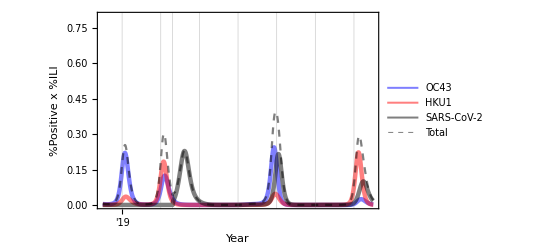

```mathematica
figinvasion
```

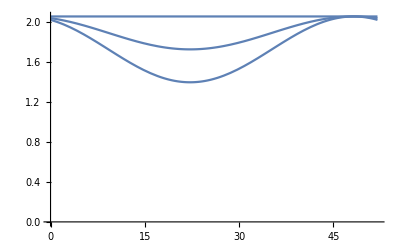

```mathematica
Plot[Table[betaval[t,f*amplitude,baseline + (1-f)*amplitude,phival,1],{f,{0, 0.5, 1}}],{t, 0, 52}, PlotRange->{0, Automatic}]
```